```mathematica
R=226.4;
frequenz={100,500,1000,5000,10000};
UppCh1={1.16,4.0,4.8,4.4,5.2};
UppCh2={190,124,76,17,8.2};
Abstand={2.5,0.5,0.26,0.050,0.025}*10^(-3)
```

{0.0025,0.0005,0.00026,0.00005,0.000025}

```mathematica
processed=Table[R*UppCh2[[i]]/(UppCh1[[i]]),{i,1,Length[UppCh2]}]
```

{37082.8,7018.4,3584.67,874.727,357.015}

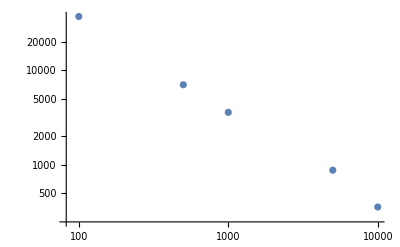

```mathematica
ListLogLogPlot[Transpose[{frequenz,processed}]]
```

```mathematica
FindFit[Transpose[{frequenz,processed}],A x^b,{A,b},x]
```

{A→4.15376×10^6,b→-1.02469}

```mathematica
Table[Abstand[[i]]*frequenz[[i]]*2,{i,1,Length[frequenz]}]
```

{0.5,0.5,0.52,0.5,0.5}

## Induktivität

```mathematica
R=14.8;
Rsp=2.4
frequenz={100,500,1000,5000,10000};
UppCh1={0.46,0.45,0.44,0.4,0.31};
UppCh2={2,9.2,18,84,130.22};
Abstand={2.8,0.475,0.26,0.050,0.024}*10^(-3)
```

2.4

{0.0028,0.000475,0.00026,0.00005,0.000024}

```mathematica
processed=Table[UppCh2[[i]]*R/(UppCh1[[i]]),{i,1,Length[UppCh2]}]
```

{64.3478,302.578,605.455,3108.,6216.95}

```mathematica
2/(0.46/14.8)
```

64.3478

```mathematica
data=Sqrt[#^2-Rsp^2]&/@processed
```

{64.3031,302.568,605.45,3108.,6216.95}

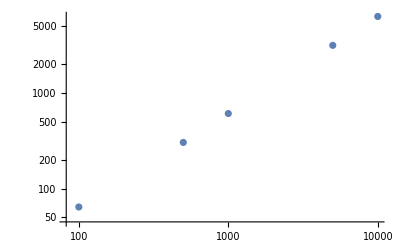

```mathematica
ListLogLogPlot[Transpose[{frequenz,data}]]
```

```mathematica
Table[Abstand[[i]]*frequenz[[i]]*2,{i,1,Length[frequenz]}]
```

{0.56,0.475,0.52,0.5,0.48}

## Induktion

```mathematica
R=14.8
frequenz={100,300,1000,3000,10000}
```

14.8

{100,300,1000,3000,10000}

```mathematica
UppR={0.44,0.44,0.44,0.44,0.31}
UppInd={0.042,0.112,0.40,1.2,3.0}
```

{0.44,0.44,0.44,0.44,0.31}

{0.042,0.112,0.4,1.2,3.}

```mathematica
processed=Table[UppInd[[i]]/UppR[[i]],{i,1,Length[UppInd]}]
```

{0.0954545,0.254545,0.909091,2.72727,9.67742}

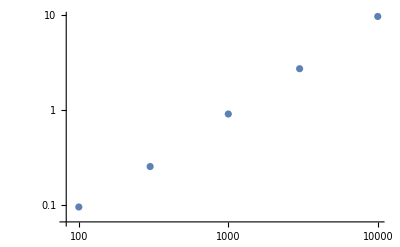

```mathematica
ListLogLogPlot[Transpose[{frequenz,processed}]]
```

```mathematica
FindFit[Transpose[{frequenz,processed}],A x^b,{A,b},x]
```

{A→0.000644318,b→1.04412}